# Load Files

```mathematica
SetDirectory[NotebookDirectory[]];

Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
Get[FileNameJoin[{Directory[],"DifferentialOperator.m"}]];
$P=2^31-1;
PureIntegrals=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasis1-111.txt"}]];

(*LaportaBasis=ReadList[FileNameJoin[{Directory[],"masters"}]];
LaportaBasis=Cases[LaportaBasis,_ptb,Infinity];*)
```

# Generate Phase-Space Point

```mathematica
(*tPoint=GetRandomPT[0,$P]
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]*)
samplepoint=1;
SubReduList=Get[ToString[StringForm["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone/KIRA/splitres/phasespace_00002.m",IntegerString[samplepoint,10,5]]]];
tPoint=Thread[Rule[invariants,SubReduList[[2,1]]]]

reductionRules=ReductionRules=GetReductionTableFromList[SubReduList[[2,2]]];


epsrepl={(ep->(4-d)/2)/.tPoint};
PureIntegralN=Expand[PureIntegrals/.tPoint/.epsrepl/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P]//EchoTiming;
diffOp=getDifferentialOperator[tPoint];
checkDifferentialOperator[tPoint,diffOp]
```

{d→100063301,mt2→2014371165,s12→869355343,s123→1019808457,s16→678417019,s23→1633776619,s234→882469038,s34→1500459823,s345→1458692992,s45→1064487363,s56→360465479}

0.210839

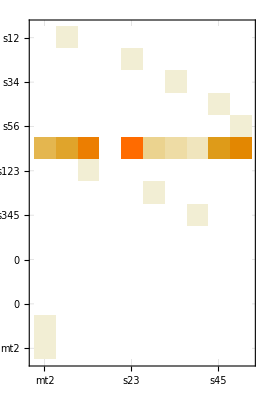

Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

∂_(RowBox[{) Δ6=0

«7 more identical outputs»

```mathematica
Cases[PureIntegralN3,_hxb,Infinity]//DeleteDuplicates//Length
NonZeros//Length
```

277

5890

# Compute Basis Change Matrix

241

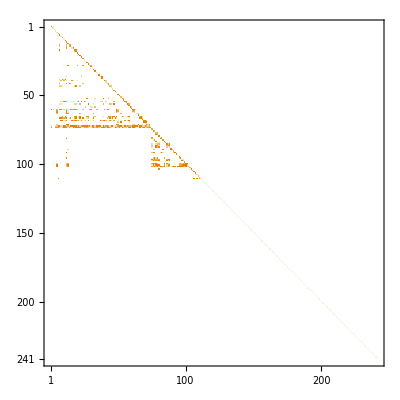

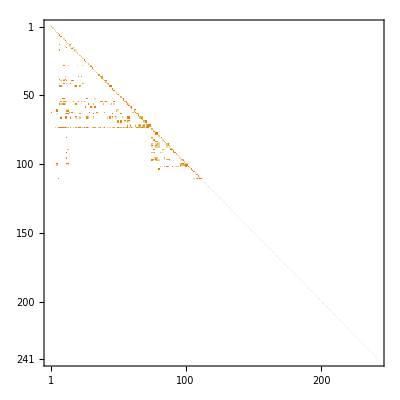

```mathematica
(*reductionRules=GetReductionTableFromFile[FileNameJoin[{NotebookDirectory[],"KIRA/results/hxb/numerics_2147483647_0.m"}]];*)
Ureduce=ReadList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];
ExtraRelations=GetExtraRelationReplacements[reductionRules,tPoint];
PureIntegralN2=Expand[PureIntegralN/.reductionRules,Modulus->$P];
PureIntegralN3=Expand[PureIntegralN2/.ExtraRelations,Modulus->$P];

NonZeros=Cases[reductionRules,_hxb,Infinity]//DeleteDuplicates;
ZeroInts=Complement[Ureduce,NonZeros];
ZeroIntsRepl=Thread[Rule[ZeroInts,0]];
PureIntegralN4=Expand[PureIntegralN3/.ExtraRelations/.ZeroIntsRepl,Modulus->$P];
Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates//Length
SubLaporta=Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates;

PureIntegralN4=Expand[PureIntegralN4/.epsrepl,Modulus->$P];

BasisChangMat=Table[CoefficientArrays[PureIntegralN4[[pos]],SubLaporta],{pos,1,Length[PureIntegralN]}];
BasisChangMat=Normal[BasisChangMat[[All,2]]];
BasisChangMatInv=Inverse[BasisChangMat,Modulus->$P];
BasisChangMat//MatrixPlot
BasisChangMatInv//MatrixPlot
```

# Compute DE Matrix Pre IBP

```mathematica
loopMomentumScalarProductsT=Expand[loopMomentumScalarProducts/.tPoint,Modulus->$P];
mandelstamScalarProductsT=Expand[mandelstamScalarProducts/.tPoint,Modulus->$P];
DeleteList=Delete[{1,2,3,4,5,6,7,8,9,10,11},Position[tPoint[[All,1]],s16]];
Monitor[diffInts=Table[
Expand[Expand[(applyDifferentialOperator[Collect[Coefficient[diffOp,ds[invariantsnodUpperCase[[var]]]],del[___]],Expand[PureIntegrals[[intpos]]/.tPoint[[DeleteCases[DeleteList,var+1]]]/.epsrepl,Modulus->$P]]/.tPoint/.root'[x_]:>1/(2 root[x]))/.root[x_]:>PowerMod[x,1/2,$P],Modulus->$P]/.loopMomentumScalarProductsT/.mandelstamScalarProductsT,Modulus->$P],{var,1,Length[invariantsnodUpperCase]},{intpos,1,Length[PureIntegrals]}],Row[{ProgressIndicator[(var-1)*241+intpos,{1,241*10}],"  ",var,"/10 ",intpos,"/241"}]];
```

## Extra Step If Redu List does not exit yet

```mathematica
ToReduce=Cases[diffInts,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}],ToReduce];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ReduList.txt"}]];

ToReduce2=Cases[PureIntegralN,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}],ToReduce2];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];

GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ExtraRelationsReduList.txt"}]];

DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
WriteJobFile[{"ExtraRelationsReduList","UReduList","ReduList"}]
```

8592

733

# Apply IBP Reduction

```mathematica
diffIntsIBREDUCED=Expand[diffInts/.reductionRules/.ExtraRelations,Modulus->$P];
NonReduced=Cases[diffIntsIBREDUCED,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
NullInts2=Complement[NonReduced,SubLaporta];
diffIntsIBREDUCED=diffIntsIBREDUCED/.Thread[Rule[NullInts2,0]];
```

499

# Compute DE Matrices

```mathematica
dhxbMatrices=Table[Normal[CoefficientArrays[diffIntsIBREDUCED[[i,j]],SubLaporta]/.{0}->{0,ConstantArray[0,Length[PureIntegralN]]}][[2]],{i,1,Length[invariants]-1},{j,1,Length[SubLaporta]}];
Mplot1=MatrixPlot[Expand[dhxbMatrices[[1]].BasisChangMatInv,Modulus->$P]];
Mplot2=MatrixPlot[Expand[dhxbMatrices[[2]].BasisChangMatInv,Modulus->$P]];
Mplot3=MatrixPlot[Expand[dhxbMatrices[[3]].BasisChangMatInv,Modulus->$P]];
Mplot4=MatrixPlot[Expand[dhxbMatrices[[4]].BasisChangMatInv,Modulus->$P]];
Mplot5=MatrixPlot[Expand[dhxbMatrices[[5]].BasisChangMatInv,Modulus->$P]];
Mplot6=MatrixPlot[Expand[dhxbMatrices[[6]].BasisChangMatInv,Modulus->$P]];
Mplot7=MatrixPlot[Expand[dhxbMatrices[[7]].BasisChangMatInv,Modulus->$P]];
Mplot8=MatrixPlot[Expand[dhxbMatrices[[8]].BasisChangMatInv,Modulus->$P]];
Mplot9=MatrixPlot[Expand[dhxbMatrices[[9]].BasisChangMatInv,Modulus->$P]];
Mplot10=MatrixPlot[Expand[dhxbMatrices[[10]].BasisChangMatInv,Modulus->$P]];
GraphicsGrid[{{Mplot1,Mplot2,Mplot3,Mplot4,Mplot5},{Mplot6,Mplot7,Mplot8,Mplot9,Mplot10}}]
```

-Graphics-

```mathematica
BasisChangMat
```

```mathematica
Position[LaportaBasis,hxb[0,0,1,1,0,0,1,0,0,0,0,0,0]]
```

{{5}}

```mathematica
BasisChangMat[[All,5]]
```

{0,0,0,0,337100971,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,899792298,1257557939,1517909673,725500337,0,0,0,0,0,0,0,636386998,688806998,1309763971,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,460736975,1750863437,1648796596,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
PureIntegrals[[8]]
Position[PureIntegralN4,hxb[0,0,1,1,0,0,1,0,0,0,0,0,0]][[All,1]]
```

((2 ep-13 ep^2+27 ep^3-18 ep^4) hxb[0,0,1,1,0,0,1,0,0,0,0,0,0])/s34

{8,40,44,55,57,61,66,67,69,73,74}

```mathematica
PureIntegralN4[[40]]
```

1330661858 hxb[-1,0,1,1,0,0,1,0,1,0,0,0,0]+1910134573 hxb[-1,1,1,1,0,0,1,0,1,0,0,0,0]+507593364 hxb[0,0,1,1,0,0,0,0,1,0,0,0,0]+933891816 hxb[0,0,1,1,0,0,1,0,0,0,0,0,0]+169575106 hxb[0,0,1,1,0,0,1,0,1,0,0,0,0]+1078951286 hxb[0,1,0,1,0,0,1,0,0,0,0,0,0]+374110145 hxb[0,1,0,1,0,0,1,0,1,0,0,0,0]+668091211 hxb[0,1,1,1,0,0,1,0,1,0,0,0,0]

```mathematica
TTjMIs=Cases[{hxb[1,0,0,1,0,0,1,0,0,0,0,0,0] # 73
hxb[0,1,0,1,0,0,1,0,0,0,0,0,0] # 74
hxb[0,1,0,1,0,0,1,0,1,0,0,0,0] # 330
hxb[1,0,0,1,0,0,0,1,0,0,0,0,0] # 137
hxb[0,1,0,1,0,0,0,1,0,0,0,0,0] # 138
hxb[-1,1,0,1,0,0,0,1,0,0,0,0,0] # 138
hxb[1,0,0,1,0,0,1,1,0,0,0,0,0] # 201
hxb[0,1,0,1,0,0,1,1,0,0,0,0,0] # 202
hxb[1,1,0,1,0,0,1,1,0,0,0,0,0] # 203
hxb[1,1,0,1,0,0,1,1,-1,0,0,0,0] # 203
hxb[0,1,0,1,0,0,1,1,1,0,0,0,0] # 458
hxb[-1,1,0,1,0,0,1,1,1,0,0,0,0] # 458},_hxb,Infinity];
```

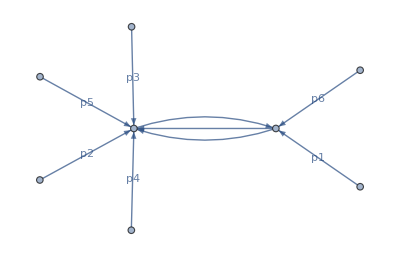

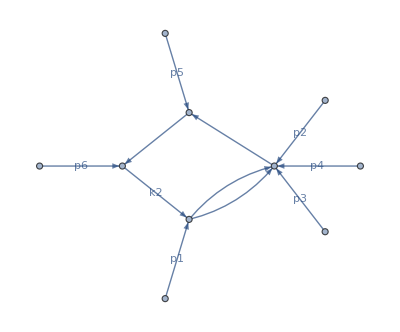

-Graphics-

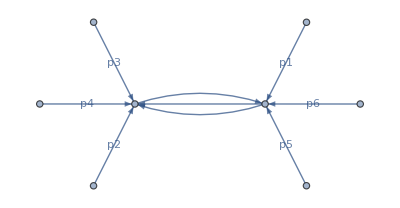

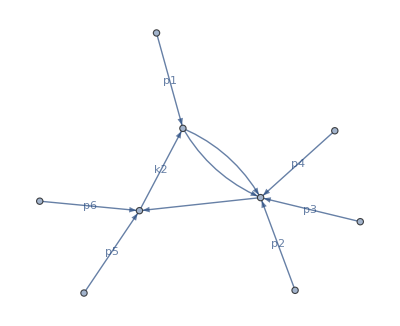

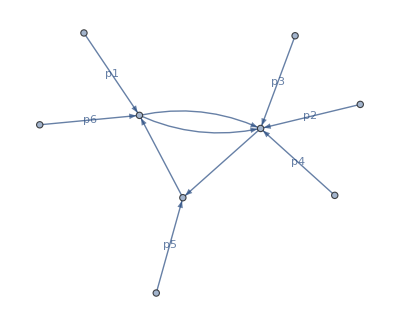

-Graphics-

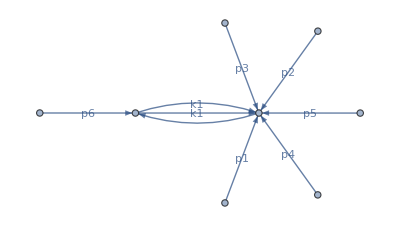

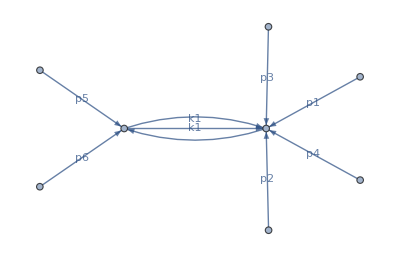

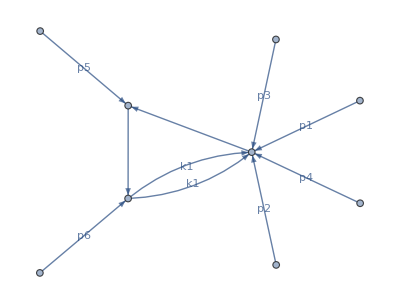

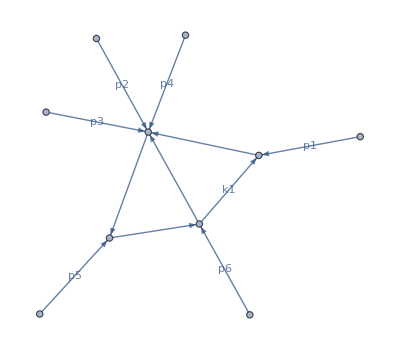

-Graphics-

```mathematica
For[i=1,i<=12,i++,
Echo[plotDiagram[TTjMIs[[i]]]]
]
```